```mathematica
ClearAll["Global`*"];

(*-------------------------------------------------------------------------*)
(*1. PARÁMETROS FUNDAMENTALES*)
(*-------------------------------------------------------------------------*)
kB=1;
hbar=1;

(*-------------------------------------------------------------------------*)
(*2. DEFINICIÓN DE LOS COEFICIENTES DE CONTRASTE *)
(*-------------------------------------------------------------------------*)

(*Caso 1:Baños con misma estadística,sistema central distinto (1,-1,1) o (-1,1,-1)*)
C1[gL_,gR_,TL_,TR_,w_]:=Abs[(gL^2-gR^2)/(gL^2+gR^2)]*Abs[(Coth[hbar*w/(2*kB*TL)]-Coth[hbar*w/(2*kB*TR)])/(Coth[hbar*w/(2*kB*TL)]+Coth[hbar*w/(2*kB*TR)])];

(*Caso 2:Baño híbrido con sistema central fermiónico (1,-1,-1)*)
C2[gL_,gR_,TL_,TR_,w_]:=Abs[Tanh[hbar*w/(2*kB*TL)]-Tanh[hbar*w/(2*kB*TR)]]/(Tanh[hbar*w/(2*kB*TL)]+Tanh[hbar*w/(2*kB*TR)]+2*(gL^2/gR^2));

(*Caso 3:Baño híbrido con sistema central bosónico (1,1,-1)*)
C3[gL_,gR_,TL_,TR_,w_]:=Abs[Coth[hbar*w/(2*kB*TL)]-Coth[hbar*w/(2*kB*TR)]]/(Coth[hbar*w/(2*kB*TL)]+Coth[hbar*w/(2*kB*TR)]+2*(gR^2/gL^2));

(*-------------------------------------------------------------------------*)
(*3. DEFINICIÓN DE LAS CONDUCTANCIAS TÉRMICAS LINEALES*)
(*-------------------------------------------------------------------------*)

(*Sistema completamente Bosónico (+1,+1,+1)*)
KappaBoson[gL_,gR_,T_,w_]:=(w^2*gL^2*gR^2)/(gL^2+gR^2)*Csch[hbar*w/(2*kB*T)]^2/(4*kB*T^2);

(*Sistema completamente Fermiónico (-1,-1,-1)*)
KappaFermion[gL_,gR_,T_,w_]:=(w^2*gL^2*gR^2)/(gL^2+gR^2)*Sech[hbar*w/(2*kB*T)]^2/(4*kB*T^2);

(*Sistema Híbrido,Central Bosónico (+1,+1,-1)*)
KappaHibridoB[gL_,gR_,T_,w_]:=(w^2*gL^2*gR^2)/(gL^2*Coth[hbar*w/(2*kB*T)]+gR^2)*Csch[hbar*w/(2*kB*T)]^2/(4*kB*T^2);

(*Sistema Híbrido,Central Fermiónico (+1,-1,-1)*)
KappaHibridoF[gL_,gR_,T_,w_]:=(w^2*gL^2*gR^2)/(gL^2+gR^2*Tanh[hbar*w/(2*kB*T)])*Sech[hbar*w/(2*kB*T)]^2/(4*kB*T^2);
```

```mathematica
(*-------------------------------------------------------------------------*)
(*4. GRÁFICAS DE CONTRASTE *)
(*-------------------------------------------------------------------------*)
wVal=1;
gRVal=1;
TRVal=10^-6; (*Equivalente numérico a TR->0 para evitar indeterminaciones*)
TLVals={1,2,5,10,50,500};
colores=ColorData["Rainbow"]/@Subdivide[0,1,Length[TLVals]-1];

plotOpts={PlotRange->{0,1.05},Frame->True,
FrameLabel->{"\!\(\*SubscriptBox[\(g\), \(L\)]\)/\!\(\*SubscriptBox[\(g\), \(R\)]\)","Contrast"},PlotLegends->LineLegend[colores,StringTemplate["TL = ``"]/@TLVals,LegendFunction->"Frame"],
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
ImageSize->Large,
PlotStyle->Directive[Thickness[0.005]]};

(*Figura 2:Misma estadística en los baños (1,-1,1)*)
fig2=LogLinearPlot[Evaluate[Table[C1[gL,gRVal,TL,TRVal,wVal],{TL,TLVals}]],{gL,0.001,100},Evaluate[plotOpts],GridLines->{{1},None},PlotLabel->"Fig 2: Same bath statistics \n (1,-1,1) or (-1,1,-1)"];

(*Figura 3(a):Baños híbridos,qubit central (1,-1,-1)*)
fig3a=LogLinearPlot[Evaluate[Table[C2[gL,gRVal,TL,TRVal,wVal],{TL,TLVals}]],{gL,0.001,100},Evaluate[plotOpts],GridLines->{{1},None},PlotLabel->"Fig 3(a): Hybrid baths, central qubit \n (1,-1,-1)"];

(*Figura 3(b):Baños híbridos,oscilador central (1,1,-1)*)
fig3b=LogLinearPlot[Evaluate[Table[C3[gL,gRVal,TL,TRVal,wVal],{TL,TLVals}]],{gL,0.001,100},Evaluate[plotOpts],GridLines->{{1},None},PlotLabel->"Fig 3(b): Hybrid baths, central oscillator \n (1,1,-1)"];

(*Mostrar todas las gráficas de contraste juntas*)
Print[GraphicsGrid[{{fig2},{fig3a},{fig3b}},ImageSize->600]];
```

-Graphics-

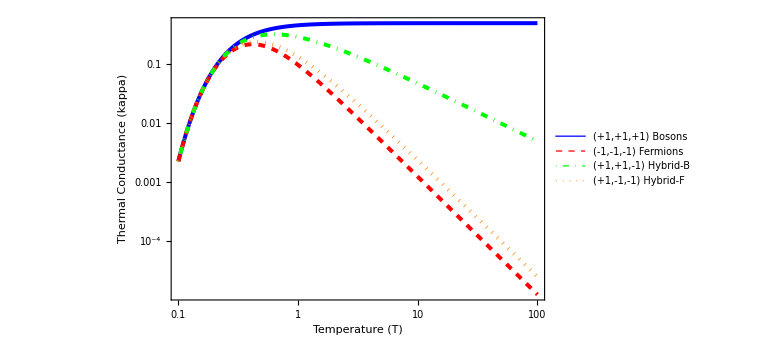

```mathematica
(*-------------------------------------------------------------------------*)
(*5. GRÁFICAS DE CONDUCTANCIA TÉRMICA*)
(*-------------------------------------------------------------------------*)

(*Fijamos los acoplamientos a la unidad para observar puramente el efecto estadístico*)
gLVal=1;
gRVal=1;

figConductancia=LogLogPlot[{
KappaBoson[gLVal,gRVal,T,wVal],
KappaFermion[gLVal,gRVal,T,wVal],
KappaHibridoB[gLVal,gRVal,T,wVal],
KappaHibridoF[gLVal,gRVal,T,wVal]},{T,0.1,100},
PlotRange->All,Frame->True,FrameLabel->{"Temperature (T)","Thermal Conductance (\!\(\*kappa\))"},PlotStyle->{Directive[Blue,Thickness[0.005]],Directive[Red,Thickness[0.005],Dashed],Directive[Green,Thickness[0.005],DotDashed],Directive[Orange,Thickness[0.005],Dotted]},
PlotLegends->LineLegend[{"(+1,+1,+1) Bosons","(-1,-1,-1) Fermions","(+1,+1,-1) Hybrid-B","(+1,-1,-1) Hybrid-F"}],
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
ImageSize->Large]
```